```mathematica
wave=Import["waveform.csv"];
```

* First column is time and the second column is the amplitude.
* As we want only amplitudes, [;; , 2]

```mathematica
ft=Fourier[wave[[;;,2]]];
```

* plotting the first 1000 points.
* Abs to take absolute values
* Transpose to get (x,y) coordinates.

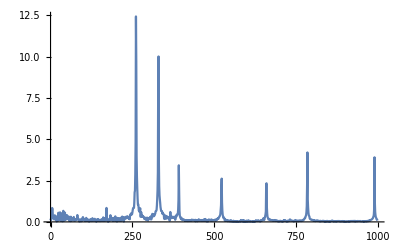

```mathematica
ListPlot[Transpose[{Table[i,{i,0,999}],Abs[ft[[1;;1000]]]}],PlotRange->All,Joined->True]
```

```mathematica
TableForm[Transpose[{Table[i,{i,0,999}],Abs[ft[[1;;1000]]]}],1000];
```

```mathematica
TableForm[{Table[i,{i,0,999}],Abs[ft[[1;;1000]]]},1000];
```